```mathematica
<< WorldPlot`
```

```mathematica
data=Rest[Import[ToFileName[NotebookDirectory[],"data.csv"],"CSV"]];
```

```mathematica
wm=WorldPlot[{World,RandomGrays}];
```

```mathematica
coords = Map[Point[{ToMinutes[#[[1]]],-1*ToMinutes[#[[2]]]}]&,data[[All,4;;5]],{1}] ;
temps = data[[All,7;;18]];
names = data[[All,1;;3]];
```

```mathematica
xdata=Join[names,Transpose[{coords,temps}],2];
```

```mathematica
kiev = 333450;
```

```mathematica
kievtemp=Select[xdata,#[[1]]==kiev &][[1,5]];
kievcoord=Select[xdata,#[[1]]==kiev &][[1,4,1]]/60;
```

```mathematica
kievdist=Map[GeoDistance[#[[4,1]]/60,kievcoord]&,xdata];
```

```mathematica
kievtdist=Map[EuclideanDistance[#[[5]],kievtemp]&,xdata];
```

```mathematica
mindist=Min[kievtdist]; maxdist=Max[kievtdist];
```

```mathematica
pc=Range[mindist,maxdist,(maxdist-mindist)/100];
```

```mathematica
near[d_] := Length[Select[kievtdist,#≤ d&]]
```

```mathematica
cnt=Map[near,pc];
```

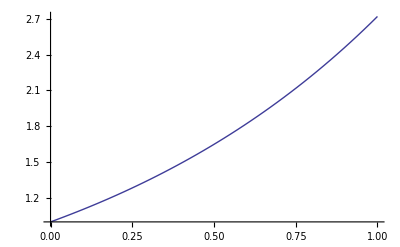

```mathematica
Plot[Exp[x],{x,0,1}]
```

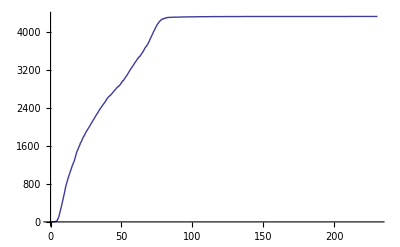

```mathematica
Plot[near[x],{x,mindist,maxdist}]
```

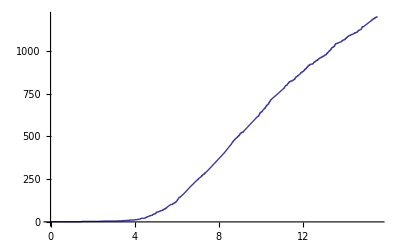

```mathematica
Plot[near[x],{x,mindist,kievtdist[[300]]}]
```

```mathematica
With[{fromstation = Select[xdata,#[[1]]==kiev &]},
Module[{ ft,dst},
ft=fromstation[[1,5]];
dst=Map[EuclideanDistance[ft,#]&,xdata[[All,5]]];
With[{ddata = Transpose[{xdata,dst}],
maxdist=Max[dst],
fp=fromstation[[1,4]]},
Manipulate[
Module[{dc,dp},
dc = Sort[Select[ddata,#[[2]]≤ distance &],#1[[2]]<#2[[2]]&];
dp=dc[[All,1,4]];
Column[{Show[{wm,
WorldGraphics[{Blue,dp}],
WorldGraphics[{Red,fp}]},ImageSize-> 800],
dc[[All,1,2;;3]]//TableView}]],
{distance,0,maxdist/10}
]]
]
]
```